```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.0 (22-Nov-2012)) loaded Thu 22 Nov 2012 11:33:19
using xCellerator 0.92 and XSSA 1204002
GPL License Terms Apply

### Create a tissue

```mathematica
T=RandomizeTemplate[TemplateRectangular[{-5,5, 2}, {-5,5, 2}],.25];
```

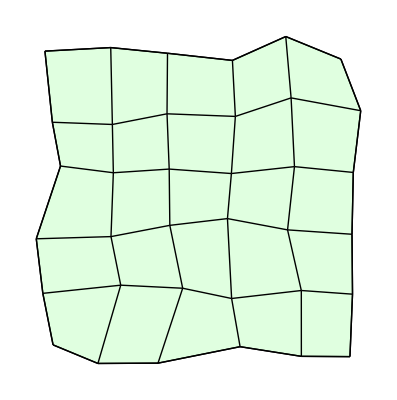

```mathematica
ShowTissue[T]
```

The tissue object has a list of vertics, followed by a list of edges, followed by a list of cells as edge numbers.

```mathematica
T
```

Tissue[{{-4.84566,-4.68014},{-3.36901,-5.29029},{-1.39124,-5.28022},{1.31143,-4.73944},{3.32858,-5.05657},{4.92842,-5.06585},{-5.18274,-2.9877},{-2.61784,-2.71927},{-0.578554,-2.81967},{1.03236,-3.15655},{3.32692,-2.89421},{5.01282,-3.01458},{-5.399,-1.19605},{-2.93908,-1.12406},{-1.00223,-0.754509},{0.895241,-0.532351},{2.87403,-0.903109},{4.99629,-1.04686},{-4.60036,1.19328},{-2.86122,0.973299},{-1.02244,1.09368},{1.02491,0.947503},{3.10152,1.1742},{5.03847,0.983123},{-4.86913,2.6318},{-2.89336,2.55896},{-1.09421,2.90891},{1.15576,2.82336},{2.99062,3.43154},{5.28329,3.01057},{-5.11363,4.96759},{-2.94724,5.08405},{-1.07823,4.89751},{1.05907,4.66265},{2.81504,5.44673},{4.62957,4.70651}},{{1,2},{1,7},{2,3},{2,8},{3,4},{3,9},{4,5},{4,10},{5,6},{5,11},{6,12},{7,8},{7,13},{8,9},{8,14},{9,10},{9,15},{10,11},{10,16},{11,12},{11,17},{12,18},{13,14},{13,19},{14,15},{14,20},{15,16},{15,21},{16,17},{16,22},{17,18},{17,23},{18,24},{19,20},{19,25},{20,21},{20,26},{21,22},{21,27},{22,23},{22,28},{23,24},{23,29},{24,30},{25,26},{25,31},{26,27},{26,32},{27,28},{27,33},{28,29},{28,34},{29,30},{29,35},{30,36},{31,32},{32,33},{33,34},{34,35},{35,36}},{{1,4,12,2},{3,6,14,4},{5,8,16,6},{7,10,18,8},{9,11,20,10},{12,15,23,13},{14,17,25,15},{16,19,27,17},{18,21,29,19},{20,22,31,21},{23,26,34,24},{25,28,36,26},{27,30,38,28},{29,32,40,30},{31,33,42,32},{34,37,45,35},{36,39,47,37},{38,41,49,39},{40,43,51,41},{42,44,53,43},{45,48,56,46},{47,50,57,48},{49,52,58,50},{51,54,59,52},{53,55,60,54}}]

### Convert to a FlatTissue

The flat tissue only has vertices and cells as vertex numbers

```mathematica
F=Tissue2FlatTissue[T]
```

FlatTissue[{{-4.84566,-4.68014},{-3.36901,-5.29029},{-1.39124,-5.28022},{1.31143,-4.73944},{3.32858,-5.05657},{4.92842,-5.06585},{-5.18274,-2.9877},{-2.61784,-2.71927},{-0.578554,-2.81967},{1.03236,-3.15655},{3.32692,-2.89421},{5.01282,-3.01458},{-5.399,-1.19605},{-2.93908,-1.12406},{-1.00223,-0.754509},{0.895241,-0.532351},{2.87403,-0.903109},{4.99629,-1.04686},{-4.60036,1.19328},{-2.86122,0.973299},{-1.02244,1.09368},{1.02491,0.947503},{3.10152,1.1742},{5.03847,0.983123},{-4.86913,2.6318},{-2.89336,2.55896},{-1.09421,2.90891},{1.15576,2.82336},{2.99062,3.43154},{5.28329,3.01057},{-5.11363,4.96759},{-2.94724,5.08405},{-1.07823,4.89751},{1.05907,4.66265},{2.81504,5.44673},{4.62957,4.70651}},{{1,2,8,7},{2,3,9,8},{3,4,10,9},{4,5,11,10},{5,6,12,11},{7,8,14,13},{8,9,15,14},{9,10,16,15},{10,11,17,16},{11,12,18,17},{13,14,20,19},{14,15,21,20},{15,16,22,21},{16,17,23,22},{17,18,24,23},{19,20,26,25},{20,21,27,26},{21,22,28,27},{22,23,29,28},{23,24,30,29},{25,26,32,31},{26,27,33,32},{27,28,34,33},{28,29,35,34},{29,30,36,35}}]

Compare the cells in the FlatTissue with the Vertex Numbers in the original tissue

```mathematica
F[[2]]
```

{{1,2,8,7},{2,3,9,8},{3,4,10,9},{4,5,11,10},{5,6,12,11},{7,8,14,13},{8,9,15,14},{9,10,16,15},{10,11,17,16},{11,12,18,17},{13,14,20,19},{14,15,21,20},{15,16,22,21},{16,17,23,22},{17,18,24,23},{19,20,26,25},{20,21,27,26},{21,22,28,27},{22,23,29,28},{23,24,30,29},{25,26,32,31},{26,27,33,32},{27,28,34,33},{28,29,35,34},{29,30,36,35}}

```mathematica
CellVertexNumbers[T]
```

{{1,2,8,7},{2,3,9,8},{3,4,10,9},{4,5,11,10},{5,6,12,11},{7,8,14,13},{8,9,15,14},{9,10,16,15},{10,11,17,16},{11,12,18,17},{13,14,20,19},{14,15,21,20},{15,16,22,21},{16,17,23,22},{17,18,24,23},{19,20,26,25},{20,21,27,26},{21,22,28,27},{22,23,29,28},{23,24,30,29},{25,26,32,31},{26,27,33,32},{27,28,34,33},{28,29,35,34},{29,30,36,35}}

### Convert the flat tissue back to the original and compare

```mathematica
Q=FlatTissue2Tissue[F];
```

```mathematica
Q==T
```

True